{0.00371348}

{0.502258}

{0.0608892}

{0.205465}

{0.0181494}

{0.0291979}

{0.00201797}

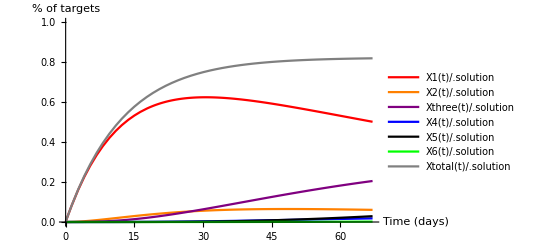

```mathematica
(*****This code has been uploaded as a.txt file to enhance readability on GitHub. To run the code in mathematica, copy and paste the text into a new mathematica notebook (.nb file). *****)

(*****This system of ODEs predicts the distribution of editing outcomes at the peCHYRON locus after 67 days of continuous editing,assuming editing efficiencies don't diminish over time. eta1 = A->B editing efficiency (%/day). eta2 = B->A editing efficiency (%/day). eta1 and eta2 were calculated with the editing_efficiency_solver_Fig3c.py script. Xwt=fraction of loci that are viable for editing, but haven't been edited yet. The initial value for Xwt is assumed to equal the maximum % edited loci observed throughout the 67-day timecourse (the percent of edited loci plateaus at 82.4%, so we assume only 82.4% of loci were viable to start with). X1=fraction of reads with 1 edit. X2=fraction of reads with 2 edits, and so forth. *****)

system={
Xviable'[t] == -eta1*Xviable[t],
X1'[t]==eta1*Xviable[t]-eta2*X1[t],
X2'[t]==eta2*X1[t]-eta1*X2[t],
Xthree'[t]==eta1*X2[t]-eta2*Xthree[t],
X4'[t]==eta2*Xthree[t]-eta1*X4[t],
X5'[t]==eta1*X4[t]-eta2*X5[t],
X6'[t]==eta2*X5[t]-eta1*X6[t],
Xtotal[t]==Xviable0-Xviable[t]};

initials={Xviable[0]==0.824,X1[0]==0,X2[0]==0,Xthree[0]==0,X4[0]==0,X5[0]==0,X6[0]==0};
fullsystem=Join[system,initials];

parameters={eta1->0.08063,eta2->0.00904, Xviable0 -> 0.824};
solution=NDSolve[fullsystem/.parameters,{Xviable[t],X1[t],X2[t],Xthree[t],X4[t],X5[t],X6[t],Xtotal[t]},{t,0,200}];

Xviable[t]/.solution/.t->67
X1[t]/.solution/.t->67
X2[t]/.solution/.t->67
Xthree[t]/.solution/.t->67
X4[t]/.solution/.t->67
X5[t]/.solution/.t->67
X6[t]/.solution/.t->67

Plot[{X1[t]/.solution,X2[t]/.solution,Xthree[t]/.solution,X4[t]/.solution,X5[t]/.solution,X6[t]/.solution,Xtotal[t]/.solution},{t,0,67},PlotRange->{0,1},PlotStyle->{{Red,Thick},{Orange,Thick},{Purple,Thick},{Blue,Thick},{Black,Thick},{Green,Thick},{Gray,Thick},{Cyan,Thick}},AxesLabel->{"Time (days)","% of targets"},PlotLegends->"Expressions"]
```